## L = 8

```mathematica
arr1= {0.88414163 , 0.96159452 , 0.96350320 , 0.95575841 , 0.95303361 , 0.95298291 , 0.95009188  };
arr2 =  {0.87760574 , 0.95757561 , 0.95861403 , 0.95776500 , 0.95015892 , 0.94979524 , 0.95239590  };
arr3 =  {0.88792931 , 0.96106931 , 0.96229792 , 0.96406682 , 0.97177861 , 0.97150915 , 0.96679927 };
arr4= {0.88744171 , 0.96280448 , 0.96444435 , 0.97202061 , 0.96375820 , 0.96337055 , 0.95515560  };
arr5 = {0.88206844 , 0.95172720 , 0.95032873 , 0.94916242 , 0.93761190 , 0.93724699 , 0.93409742  };
```

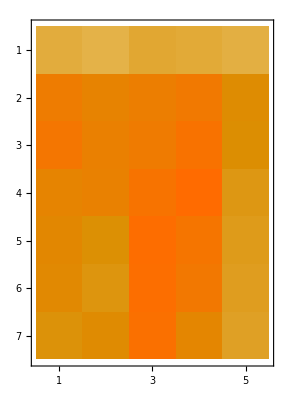

```mathematica
mat = Transpose [{arr1,arr2,arr3,arr4,arr5}];
MatrixPlot[mat]
```

```mathematica
nc = 7;
yt = Mean [mat [[nc]] ]
del = StandardDeviation [mat[[nc]]]/Sqrt [Length [mat[[nc]]]]
```

0.951708

0.00525761

```mathematica
arr1={1.87765942 , 1.88054218 , 1.88029513 , 1.88086406 };
arr2= {1.87533767 , 1.87813396 , 1.87811169 , 1.87850202 };
arr3 = {1.87761463 , 1.88022681 , 1.88029060 , 1.88067705 };
arr4={1.87754434 , 1.88028642 , 1.88028563 , 1.88071465 };
arr5 ={1.87493716 , 1.87759122 , 1.87771956 , 1.87812502 };
```

{{1.87766,1.87534,1.87761,1.87754,1.87494},{1.88054,1.87813,1.88023,1.88029,1.87759},{1.8803,1.87811,1.88029,1.88029,1.87772},{1.88086,1.8785,1.88068,1.88071,1.87813}}

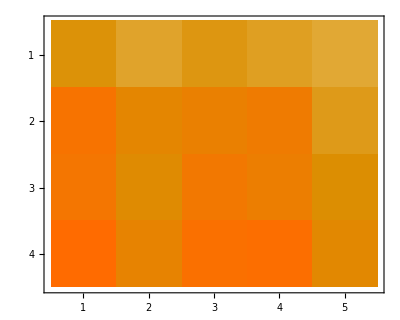

```mathematica
mat = Transpose [{arr1,arr2,arr3,arr4,arr5}]
MatrixPlot[mat]
```

```mathematica
nc = 4;
yh = Mean [mat[[nc]]]
del = StandardDeviation [mat[[nc]]]/Sqrt [Length[mat[[nc]]]]
```

1.87978

0.000601065

## L = 16

```mathematica
arr1= {0.88414163 , 0.96159452 , 0.96350320 , 0.95575841 , 0.95303361 , 0.95298291 , 0.95009188  };
arr2 =  {0.87760574 , 0.95757561 , 0.95861403 , 0.95776500 , 0.95015892 , 0.94979524 , 0.95239590  };
arr3 =  {0.88792931 , 0.96106931 , 0.96229792 , 0.96406682 , 0.97177861 , 0.97150915 , 0.96679927 };
arr4= {0.88744171 , 0.96280448 , 0.96444435 , 0.97202061 , 0.96375820 , 0.96337055 , 0.95515560  };
arr5 = {0.88206844 , 0.95172720 , 0.95032873 , 0.94916242 , 0.93761190 , 0.93724699 , 0.93409742  };
```

```mathematica
mat = Transpose [{arr1,arr2,arr3,arr4,arr5}];
MatrixPlot[mat]
```

-Graphics-

```mathematica
nc = 7;
yt = Mean [mat [[nc]] ]
del = StandardDeviation [mat[[nc]]]/Sqrt [Length [mat[[nc]]]]
```

0.951708

0.00525761

```mathematica
arr1={1.87765942 , 1.88054218 , 1.88029513 , 1.88086406 };
arr2= {1.87533767 , 1.87813396 , 1.87811169 , 1.87850202 };
arr3 = {1.87761463 , 1.88022681 , 1.88029060 , 1.88067705 };
arr4={1.87754434 , 1.88028642 , 1.88028563 , 1.88071465 };
arr5 ={1.87493716 , 1.87759122 , 1.87771956 , 1.87812502 };
```

```mathematica
mat = Transpose [{arr1,arr2,arr3,arr4,arr5}]
MatrixPlot[mat]
```

{{1.87766,1.87534,1.87761,1.87754,1.87494},{1.88054,1.87813,1.88023,1.88029,1.87759},{1.8803,1.87811,1.88029,1.88029,1.87772},{1.88086,1.8785,1.88068,1.88071,1.87813}}

-Graphics-

```mathematica
nc = 4;
yh = Mean [mat[[nc]]]
del = StandardDeviation [mat[[nc]]]/Sqrt [Length[mat[[nc]]]]
```

1.87978

0.000601065